# Project Report II - Logan Houchens and Brian Carlson

## 1.Updated Project Proposal

## General Idea

Our idea is to analyze and make predictions from social media data. We hope to analyze information that we pull from public posts to make predictions about the gender of the person posting, region/state/city of the United States that they are from, and the periodicity of posts made.  

Note: Dr. Hahn plays a large role in what we choose to do. He mentors our processes of anaylzing the data we are able to pull out from SocialMediaData. We meet every Wednesday to discuss our progress. He has focused us more on certain aspects such as simply being able to compare two data factors in the program or being able to predict gender, location, etc. of a person posting on Facebook.

## Finished Appearance

### Screen View

We plan to have our project displayed in a graphical user interface with drop-down boxes, menu screens, and easy-to-use analytical tools.

1.) The finished project, Verbum Usus (Meaning “Word Usage” in Latin) (1.) will open in a new window, bringing up the title screen (See Diagram I). On the title screen, the user has the option to select Facebook or Twitter (hopefully adding Instagram, LinkedIn, and GooglePlus) from the drop down box (2.) to analyze using the tools provided on the next screen. The “Begin” button (3.) will take the user to the next screen (II).

2.) The Tool Menu (Diagram II) will have a drop down box (1.) for choosing past trends to compare, including, but not limited to: word usage for each gender, periodicity of word usage, and word usage in certain locations. When “Compare” is clicked, the user will be taken to the “Compare” window (III). If the user wishes to know the methods we used to extract data and the way we predicted things, he/she can click on the “Explanations and Methods” button (2.) to go to the “Explanations and Methods”. The user can click “Predict” after selecting an option from the dropdown box (3.) to go to the prediction screen to select parameters for determining the option they selected. Also included in this display is a graph (4.) randomly chosen from a list of plots showing some information pulled from the selected social network.

Note: “Predict” can predict gender, location and possibly future times words will be used. Also periodicity of word usage means day of the week, time of the day, and location where a certain word is used.

3.) The Compare window (III) will have drop down boxes similar to (1.) and (2.) for specifying what you’d like to compare. Also included will be a filter for selecting a range of dates to pull posts from (3.) and the number of public users to randomly select which is done by using RandomSample through a Range of data we collect regularly. (4.). When finished, clicking the “Compute” button will take the user to the “Results” screen (IV).

4.) The Results screen (IV) will have the corresponding graphs to appropriately display the data we processed (1.). Each type of comparision will have the most important information shown relevant to that comparision (2.). The resulting statistical information (RSquared values, equation/algorithms, standard deviation, and prediction confidence) can be accessed by clicking on the button wit the same name. (3.) The results can be saved by clicking the “Save” button. (4.)

#### Click Flow

This is a graph of the screen changes that will take place within our program.

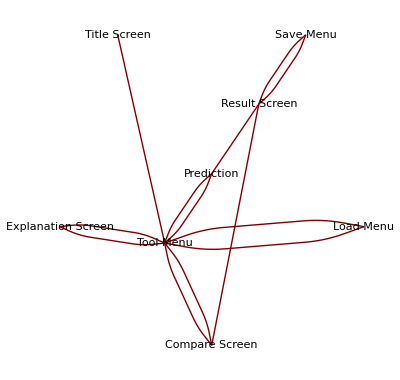

## Goals

### Increments

#### 1.

1.) Get authorization from the Institutional Review Board to study human beings.
2.) Write functions to anonymize Facebook/Twitter user data.
3.) Write functions to access individual parts of data.
4.) Complete online sensitivity training while working with people’s personal information.

#### II.

1.) Combine functions written in increment I so we can easily analyze information gathered.
2.) Analyze information and write an algorithm to predict future outcomes.
3.) Develop a new data set to test our algorithm in medium to small sized test groups.

#### III.

1.) Write a GUI format for the individual functions we create to come together into one.
2.) Make program easily accessible for user to interact with the program.
3.) Completely polish entire project for presentations.
4.) Thouroughly test our algorithm further with large test groups.

## 2.Updated Future Schedule

Week of 4/28/14:
Finish forming a database for accurate analysis of large sets of data. Finish the predict algorithm based upon our findings from analysis of our database. Work on data visualization.

Week of 5/5/14:
Finish and connect GUI to our existing algorithms and research. Possibly expand to multiple social media sites. Explore these avenues for possible new connections and further research that can be done with our code.

Week of 5/12/14:
Possibly add more connections of the data depending on Dr. Hahn’s input/advice. At this point we could start to make a presentable info section that shows our findings and such. This week is dedicated more to finishing anything we don’t already have polished if needed (hopefully not).

## 3.Research and Development Algorithm Explanations

Our project’s aim is to gain an understanding into how males and females interact with each other through various social media outlets, specifically Facebook. Work has been done showing correlation between word usage and gender, but none, that we know of, has been done in this particular area. Some important algorithms specific to this research involve our system of assigning a correlation coefficient to each word. To do that, we multiply the probability of a word occuring based on our set p(word) =  (occurances of the word)/(total number of words) and the probability of a specific gender interaction for a certain word p(gender interaction | word) = (occurance of gender interaction for word)/(occurances of the word) to get a simplified formula weight = (occurance of gender interaction for word)/(total number of words).

## 4.Description of files and file structure

We have an attatched .txt file we will be using as a database. Users can add to this database when running through our program. We use the functions Import and Export for use of this file. This .txt file is the only external file we plan to use in tandem with our code. This database may be changed to a .csv file for ease of comparison but that will be the only change.

## 5.Description of major data structures

A very large portion of our project was sorting through large amounts of messy data that the function SocialMediaData gives us. Just a couple obstacles we faced were those of sorting out unnecessary information, finding patterns of how the data is given, and sorting through the data efficiently and in a timely manner. The first two problems were eventually figured out, but the third we are still trying to figure out. As of now our major problem has been going through enough data to make accurate representations of the data set as a whole while also being fast doing so.

-Graphics-

Above is a screen-grab of how the data is given to us before we clean it up.

Below is the data after we have cleaned it up a bit.

-Graphics-

## 6.Overview of how code approaches the problem

Our code provides a tool for analyzing word usage in gender interactions and a way to predict gender interactions given a string. We take posts from public social media accounts, and, for each user, filter out everything but statuses and read the comments from each status update. With those comments, we have grouped together the gender of the status maker and the comment maker with each word of the comment, then group together the data from each user and count the frequency of each type of gender interaction for each word. From that data, we can get a coefficient that gives the strength of the correlation between each type of word and a specific gender interaction.

## 7.Description of what has been accomplished

We have mainly been working on anoymizing data and “cleaning up” the data we recieve from Facebook through SocialMediaData. What we have discovered is that it is very difficult to sift through large chunks of data to find exactly what you are looking for. So mainly our functions account for cleansing the data and anonymizing the users within the data so we can conduct legitimate research with Dr. Hahn and the Institutional Review Board which makes sure our data collection is not breaking any rules. With this consideration of the IRB and their processes much of our time has been taken out with the online class we must take. There are multiple modules we must complete and each module takes about an hour and a half to complete. In total there are ten modules so, as you can see, this has been very time consuming. We have begun on the GUI but are putting off connecting it to our GUI because it is not neccesary for our project to be succesful. 

We have also began working on creating a database that goes along with our project so anyone who has our program can run it and contribute to the database and further the research. This makes everything easier as the program does not need to be run once for a very long amount of time to get our results but can be constantly added to in short runs. While we have been doing this we also have started analyzing small sets of data with Dr. Hahn to find interesting patterns of speech from our sorted data. With our findings we have created an algorithm with Dr. Hahn to weight each word to give a number we can look at for significance in relation to the data set as a whole. Finally from our small runs and our weighting system we have begun creating a predict function using for now just our small runs to base it off of but in the future we will connect it to our database to make a more accurate prediction.

## 8.Explanation of how to get code to run

We have a lot of information that needs to be processed and handled with our project, making the run time very long. Also, since our program relies on extracting information from the social media accounts, an internet connection is needed to run.

To begin, go to Facebook in your default internet browser and log in with the username/email as “john6174doe@gmail.com” and the password as “socialmediaanalysis” and leave the page open.

To see the results of many functions at once:  Open up the file labeled “Verbum Usus” and evaluate the notebook. When a window labeled “Social Media Authentication” comes up, click on the button labeled “Sign into Facebook”. You should be taken to a window in your internet browser with an authentication code. Copy that code and paste it into the window open in Mathematica and click “Done”. The rest of the notebook should evaluate after this.

When finished, log out of Facebook by clicking the drop down arrow on the upper right of the screen and clicking “log out”.

## 9.Signed statements

Each of our signed statements are attached.